# Functions to help with the exam

#### Plotting

```mathematica
Functions
```

plotinator
Plots functions with labeled key points. For the values of key points and asymptotes, hover you mouse over them.
The syntax is basically the same as Plot however it does not accept extra arguments like plot range

```mathematica
plotinator[function,{variable,min,max}]
plotinator[{function1,function2,...},{variable,min,max}]
```

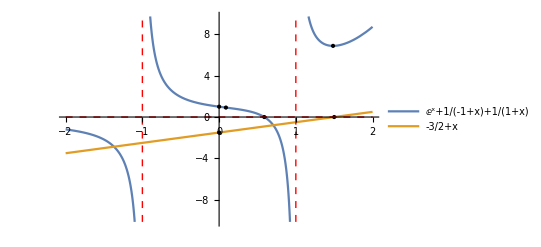

```mathematica
plotinator[{ⅇ^x+1/(x-1)+1/(x+1),x-3/2},{x,-2,2}]
```

#### Probability

plotNormalDistributionBetween
Plots probability density functions and shades the desired area. The by default the function will show 4 standard deviations either side of the mean. Supplying standardDeviationsToShow parameter can change this

```mathematica
plotNormalDistributionBetween[mean,standardDeviation,min,max]
plotNormalDistributionBetween[mean,standardDeviation,min,max,standardDeviationsToShow]
```

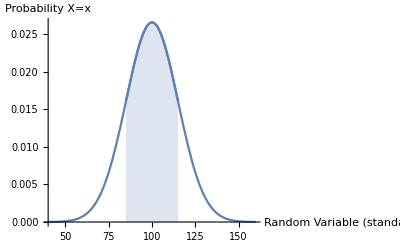

```mathematica
plotNormalDistributionBetween[100,15,85,115]
```

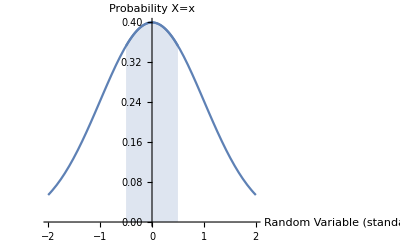

```mathematica
plotNormalDistributionBetween[0,1,-0.5,0.5,2]
```

plotNormalDistributionGreaterThan
Plots probability density functions and shades the desired area. The by default the function will show 4 standard deviations either side of the mean. Supplying standardDeviationsToShow parameter can change this. The standardDeviationsToShow parameter is the same as in plotNormalDistributionBetween.

```mathematica
probabilityNormalDistributionGreaterThan[mean,standardDeviation,min]
probabilityNormalDistributionGreaterThan[mean,standardDeviation,min,standardDeviationsToShow]
```

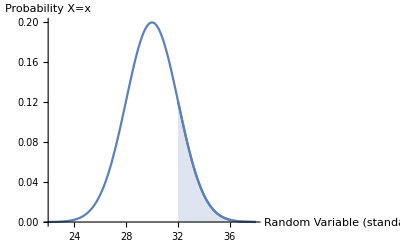

```mathematica
plotNormalDistributionGreaterThan[30,2,32]
```

plotNormalDistributionLessThan
Plots probability density functions and shades the desired area. The by default the function will show 4 standard deviations either side of the mean. Supplying standardDeviationsToShow parameter can change this. The standardDeviationsToShow parameter is the same as in plotNormalDistributionBetween.

```mathematica
plotNormalDistributionLessThan[mean,standardDeviation,max]
plotNormalDistributionLessThan[mean,standardDeviation,max,standardDeviationsToShow]
```

```mathematica
plotNormalDistributionLessThan[200,50,225]
```

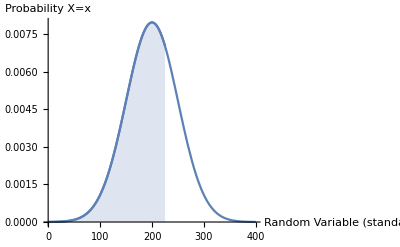

Complex Numbers (spesh)

complexPlot
Plots regions of the complex plain. The variable represents the complex number for which the region is define as the set of solutions. Most commonly the variable is z.

```mathematica
complexPlot[equasion,variable,{xmin,xmax},{ymin,ymax}]
```

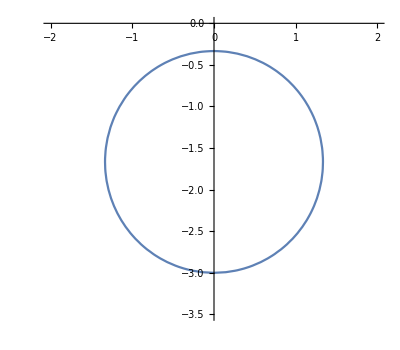

```mathematica
complexPlot[Norm[z-ⅈ]==2Norm[z+ⅈ],z,{-2,2},{-3.5,0}]
```

#### Euler’s Method (spesh)

eulersMethodPlot
Plots the eulers method approximation along with the correct solution from DSolve. The gradient should NOT include y’[x]==.

```mathematica
eulersMethodPlot[gradient,{x,xmin,xmax},y,{x0,y0},increment]
```

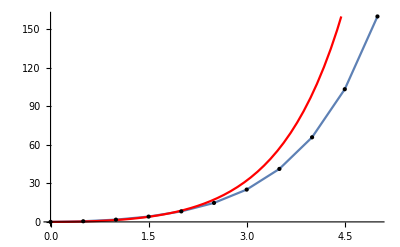

```mathematica
eulersMethodPlot[2x+y,{x,0,5},y,{0,0},0.5]
```

#### Plotting vectors (spesh)

geogebra3DSeption
Plots vectors like Geogebra. There is not way to plot planes or equations in this version. Clicking and dragging will rotate the view. Holding control while clicking and dragging will scale the view. Holding shift while clicking and dragging will scale the view.

```mathematica
geogebra3DSeption[vectors]
```

```mathematica
geogebra3DSeption[{{{0,0,0},{3,4,5}},vectorOrigin[2,1,3],vectorFrom[2,3,1,-1,2,3]}]
```

-Graphics3D-

```mathematica
Manipulate[geogebra3DSeption[{vectorOrigin[1,1,0],vectorOrigin[-1,a,0]}],{a,-1,1}]
```

### Other

clearEverything
Clears EVERYTHING the user defined. ClearAll does not do this. ClearAll only clears what you put in it. This will clear variables, functions, things you accidentally defined that are causing errors.

```mathematica
clearEverything[]
```

resetMathematica
Quits the kernel and starts a new one. Should do the same as aborting evaluation and then using clearEverything however Mathematica is weird and this is more likely to stop errors.

```mathematica
resetMathematica[]
```

Actual Code
You must shift enter ALL of the code

```mathematica
clearEverything[]:=Clear["Global`*"]
resetMathematica[]:=Module[{},Quit[];x=0;Clear[x];]
vectorOrigin[i_,j_,k_]:={{0,0,0},{i,j,k}}
vectorFrom[i0_,j0_,k0_,i1_,j1_,k1_]:={{i0,j0,k0},{i1,j1,k1}}
vector[i_,j_,k_]:={i,j,k}
geogebra3DSeption[vec_]:=Module[{i,j,maxRange,d,arrows},
maxRange=0;
d=0;
arrows={};
For[i=1,i≤Length[vec],i++,
AppendTo[arrows,Arrow[vec[[i]]]];
For[j=1,j≤3,j++,
d=Abs[vec[[i,2,j]]-vec[[i,1,j]]];
If[d>maxRange,
maxRange=d;
];
];
];
Return[
Graphics3D[arrows,Axes->{1,1,1},AxesOrigin->{0,0,0},AxesStyle->{Directive[Red,Thick],Directive[Green,Thick],Directive[Blue,Thick]},PlotRange->{{-maxRange,maxRange},{-maxRange,maxRange},{-maxRange,maxRange}}]
];
];
eulersMethod[grad_,y_,x_,increment_,startx_,starty_,endx_,showEvery_:1]:=Module[{i,previousx,previousy,output,count},
output={};
previousx=startx;
previousy=starty;
i=startx;
count=0;
AppendTo[output,{previousx,previousy}];
While[i<endx,
previousx+=increment;
previousy+=increment*(grad/.y[x]->previousy/.x->previousx);
If[Or[Mod[count,showEvery]==0,i+increment≥endx,i==startx],
AppendTo[output,{previousx,previousy}];
];
i+=increment;
count+=1;
];
Return[output];
];
eulersMethodPlot[grad_,dom_,y_,initialCondition_,interval_]:=Module[{gradxy,var,correctSolution,iceq,correctPlot,approximation,approxPlot},
var=dom[[1]];
gradxy=grad/.y->y[var];
iceq=y[initialCondition[[1]]]==initialCondition[[2]];
correctSolution=DSolve[{y'[var]==gradxy,iceq},y[var],var];

approximation=eulersMethod[gradxy,y,var,interval,initialCondition[[1]],initialCondition[[2]],dom[[3]]];
approxPlot=ListLinePlot[approximation,Epilog->{PointSize[Medium],Point[approximation]}];
correctPlot=Plot[correctSolution[[All,1,2]],dom,PlotRange->PlotRange[approxPlot],PlotStyle->Red];
Return[Show[approxPlot,correctPlot]];
];
complexPlot[f_,z_,dom_,ran_]:=ContourPlot[Evaluate[f/.z->(x+ⅈ*y)],{x,dom[[1]],dom[[2]]},{y,ran[[1]],ran[[2]]},Frame->False,Axes->True,AspectRatio->Automatic]
probabilityNormalDistributionBetween[mean_,stdev_,a_,b_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,b},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[a<x<b,x\[Distributed]NormalDistribution[mean,stdev]]];
];
probabilityNormalDistributionGreaterThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,mean+stdev*numberOfStdevToShow},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[a<x,x\[Distributed]NormalDistribution[mean,stdev]]];
];
probabilityNormalDistributionLessThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,a},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[x<a,x\[Distributed]NormalDistribution[mean,stdev]]];
];
plotNormalDistributionBetween[mean_,stdev_,a_,b_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,b},Filling->Axis,PlotRange->PlotRange[plot1]];
Return[Show[plot1,plot2]];
];
plotNormalDistributionGreaterThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,mean+stdev*numberOfStdevToShow},Filling->Axis,PlotRange->PlotRange[plot1]];
Return[Show[plot1,plot2]];
];
plotNormalDistributionLessThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,a},Filling->Axis,PlotRange->PlotRange[plot1]];
Return[Show[plot1,plot2]];
];
Zip[a_,b_]:=Module[{i, output},
output={};
For[i=1,i≤Length[a],i++,
AppendTo[output,{a[[i]],b[[i]]}];
];
Return[output];
];
roots[f_,x_,sdom_:True]:=Module[{i,rawSol,root,output},
rawSol=Solve[f==0&&sdom,x,Reals];
root={};
output={};
For[i=1,i≤Length[rawSol],i++,
If[rawSol[[i,1,2,0]]==Root,
AppendTo[root,N[rawSol[[i]],2]];
Continue[];
];
AppendTo[root,rawSol[[i]]];
];
If[Or[root=={{}},root=={}],
Return[{}],
For[i=1,i≤Length[root],i++,
AppendTo[output, {root[[i,1,2]],0}];
];
Return[output]
];
];
approximateRoots[solutions_]:=Module[{i, output},
output={};
For[i=1,i≤Length[solutions],i++,
If[solutions[[i,1,2,0]]==Root,
AppendTo[output, N[solutions[[i]],2]];
Continue[];
];
AppendTo[output, solutions[[i]]];
];
Return[output];
];
turningPoints[f_,x_,sdom_:True]:=Module[{solveResult,skippedIfStatment},
skippedIfStatment=True;
If[D[f,x]==0,
skippedIfStatment=False;
solveResult={{}};
];
If[skippedIfStatment,
solveResult=approximateRoots[Solve[D[f,x]==0&&sdom,x,Reals]];
];
If[Or[solveResult=={{}},solveResult=={}],
Return[{}]
,
Return[Zip[solveResult[[All,1,2]],f/.x->solveResult[[All,1,2]]]]
];
Print["The answer is liable to contain errors"];
Return[{}]
];
maximumTurningPoints[f_,x_,sdom_:True]:=Module[{i,TPs,output},
TPs=turningPoints[f,x,sdom];
output={};
If[Or[TPs=={{}},TPs=={},TPs=={}],
Return[{}];
];
For[i=1,i≤Length[TPs],i++,
If[(D[f,{x,2}]/.x->TPs[[i,1]])<0,
AppendTo[output,TPs[[i]]];
];
];
Return[output];
];
minimumTurningPoints[f_,x_,sdom_:True]:=Module[{i,TPs,output},
TPs=turningPoints[f,x,sdom];
output={};
If[Or[TPs=={{}},TPs=={},TPs=={}],
Return[{}];
];
For[i=1,i≤Length[TPs],i++,
If[(D[f,{x,2}]/.x->TPs[[i,1]])>0,
AppendTo[output,TPs[[i]]];
];
];
Return[output];
];
stationaryPointsOfInflection[f_,x_,sdom_:True]:=Module[{i,j,secondDSolutions,thirdDSolutions,output,inflections,shouldAdd,skippedIfStatment},
output={};
inflections={};
shouldAdd=True;
skippedIfStatment=True;
If[D[f,{x,2}]==0,
secondDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
secondDSolutions=approximateRoots[Solve[D[f,{x,2}]==0&&sdom,x,Reals]];
];
skippedIfStatment=True;
If[D[f,{x,3}]==0,
thirdDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
thirdDSolutions=approximateRoots[Solve[D[f,{x,3}]==0&&sdom,x,Reals]];
];
If[Or[secondDSolutions=={{}},secondDSolutions=={}],
Return[{}];
,
If[Or[thirdDSolutions=={{}},thirdDSolutions=={}],
Return[{}];
,
For[i=1,i≤Length[secondDSolutions],i++,
shouldAdd=False;
For[j=1,j≤Length[thirdDSolutions],j++,
If[secondDSolutions[[i]]==thirdDSolutions[[j]],
shouldAdd=True;
];
];
If[shouldAdd,
AppendTo[inflections,secondDSolutions[[i]]];
];
];
Return[Zip[inflections[[All,1,2]],f/.x->inflections[[All,1,2]]]];
];
];
Print["The answer is liable to contain errors"];
Return[{}];
];
movingPointsOfInflection[f_,x_,sdom_:True]:=Module[{i,j,secondDSolutions,thirdDSolutions,output,inflections,shouldAdd,skippedIfStatment},
output={};
inflections={};
shouldAdd=True;
skippedIfStatment=True;
If[D[f,{x,2}]==0,
secondDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
secondDSolutions=approximateRoots[Solve[D[f,{x,2}]==0&&sdom,x,Reals]];
];
skippedIfStatment=True;
If[D[f,{x,3}]==0,
thirdDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
thirdDSolutions=approximateRoots[Solve[D[f,{x,3}]==0&&sdom,x,Reals]];
];
If[Or[secondDSolutions=={{}},secondDSolutions=={}],
Return[{}];
,
If[Or[thirdDSolutions=={{}},thirdDSolutions=={}],
Return[Zip[secondDSolutions[[All,1,2]],f/.x->secondDSolutions[[All,1,2]]]];
,
For[i=1,i≤Length[secondDSolutions],i++,
shouldAdd=True;
For[j=1,j≤Length[thirdDSolutions],j++,
If[secondDSolutions[[i]]==thirdDSolutions[[j]],
shouldAdd=False;
];
];
If[shouldAdd,
AppendTo[inflections,secondDSolutions[[i]]];
];
];
Return[Zip[inflections[[All,1,2]],f/.x->inflections[[All,1,2]]]];
];
];
Print["The answer is liable to contain errors"];
Return[{}];
];
concaviteAtPointAsInteger[f_,x_,p_]:=Module[{secondD},
secondD=D[f,{x,2}];
If[(secondD/.x->p)≤0,
Return[1]
,
Return[-1]
];
Return["Error"];
];
yIntercepts[f_,x_,sdom_:True]:=Module[{},
If[(f&&sdom/.x->0)==False,
Return[{}];
];
Return[{{0,(f&&sdom/.x->0)}}];
];
evalulateValue[val_]:=val
plotColors[n_]:=ColorData[97,"ColorList"][[Mod[n,15]]]
obliqueAsymptote[f_,x_]:=Module[{i,expandedForm,temp,output,hasOAsymptote},
expandedForm=Expand[f];
If[expandedForm[[0]]==Plus,
temp={};
output={};
hasOAsymptote=False;
For[i=1,i≤Length[expandedForm],i++,
If[Limit[expandedForm[[i]],x->∞]≠0,
AppendTo[temp,expandedForm[[i]]];
,
hasOAsymptote=True;
];
];
hasOAsymptote=True;
If[hasOAsymptote,
temp=Total[temp];
AppendTo[output,temp];
If[temp==0,output=Drop[output,-1]];
temp={};
];
hasOAsymptote=False;
For[i=1,i≤Length[expandedForm],i++,
If[Limit[expandedForm[[i]],x->-∞]≠0,
AppendTo[temp,expandedForm[[i]]];
,
hasOAsymptote=True;
];
];
hasOAsymptote=True;
If[hasOAsymptote,
temp=Total[temp];
AppendTo[output,temp];
If[temp==0,output=Drop[output,-1]];
temp={};
];
output=DeleteDuplicates[output];
Return[output];
];
Return[{}];
];
valueOfInequality[inequ_,x_]:=Module[{},
If[inequ[[2]]==x,Return[inequ[[1]]]];
If[inequ[[1]]==x,Return[inequ[[2]]]];
]
verticleAsymptotes[f_,x_]:=Module[{i,j,dom,asymptotes,output},
dom=FunctionDomain[f,x];
asymptotes={};
output={};
For[i=1,i≤Length[dom],i++,
If[dom[[i,0]]==Less,
AppendTo[asymptotes,valueOfInequality[dom[[i]],x]];
];
If[dom[[i,0]]==Greater,
AppendTo[asymptotes,valueOfInequality[dom[[i]],x]];
];
If[dom[[i,0]]==Inequality,
For[j=1,j≤Length[dom[[i]]]-2,j=j+2,
AppendTo[asymptotes,valueOfInequality[dom[[i,j;;j+2]],x]];
];
];
];
asymptotes=DeleteDuplicates[asymptotes];
For[i=1,i≤Length[asymptotes],i++,
If[Or[Limit[f,x->asymptotes[[i]],Direction->"FromAbove"]==∞,Limit[f,x->asymptotes[[i]],Direction->"FromAbove"]==-∞],
AppendTo[output,asymptotes[[i]]];
];
If[Or[Limit[f,x->asymptotes[[i]],Direction->"FromBelow"]==∞,Limit[f,x->asymptotes[[i]],Direction->"FromBelow"]==-∞],
AppendTo[output,asymptotes[[i]]];
];
];
output=DeleteDuplicates[output];
Return[output];
];
horizontalAsymptotes[f_,x_]:=Module[{output,val},
output={};
val=0;
val=Limit[f,x->∞];
If[And[val≠∞,val≠-∞],
AppendTo[output,val];
];
val=Limit[f,x->-∞];
If[And[val≠∞,val≠-∞],
AppendTo[output,val];
];
output=DeleteDuplicates[output];
Return[output];
];
plotinator[f_,dom_,showObliqueAsymptotes_:False]:=Module[{i,j,keyPoints,plot,absoluteRange,epilogPoints,epologTextOffset,epilogs,hAsymptotes,vAsymptotes,oAsymptotes,asymptotes,solveDomain,plotEquasions,oAsymptoteHolder,plotStyle,pointObjects,numberOfEquasions},
keyPoints={};
plot=0;
absoluteRange=0;
epilogPoints=0;
epologTextOffset=0;
epilogs={};
solveDomain=dom[[2]]≤dom[[1]]≤dom[[3]];
plotEquasions={f};
oAsymptoteHolder={};
plotStyle={};
pointObjects={};
numberOfEquasions=0;

If[(f)[[0]]==List,
plotEquasions=f;
];

For[i=1,i≤Length[plotEquasions],i++,
AppendTo[plotStyle,{plotColors[i]}]
];
For[i=1,i≤Length[plotEquasions],i++,
keyPoints=Join[keyPoints,movingPointsOfInflection[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,stationaryPointsOfInflection[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,turningPoints[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,roots[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,yIntercepts[plotEquasions[[i]],dom[[1]],solveDomain]];
];
keyPoints=DeleteDuplicates[keyPoints];

plot=Plot[f,dom];
absoluteRange=Abs[PlotRange[plot][[2,2]]-PlotRange[plot][[2,1]]];
For[j=1,j≤Length[plotEquasions],j++,
For[i=1,i≤Length[keyPoints],i++,
epologTextOffset=1/10*absoluteRange*concaviteAtPointAsInteger[plotEquasions[[j]],dom[[1]],keyPoints[[i,1]]];
AppendTo[epilogs,Text[keyPoints[[i]],{keyPoints[[i,1]],keyPoints[[i,2]]+epologTextOffset}]];
];
];

asymptotes={};
For[j=1,j≤Length[plotEquasions],j++,
hAsymptotes=horizontalAsymptotes[plotEquasions[[j]],dom[[1]]];
vAsymptotes=verticleAsymptotes[plotEquasions[[j]],dom[[1]]];
oAsymptotes=obliqueAsymptote[plotEquasions[[j]],dom[[1]]];
For[i=1,i≤Length[hAsymptotes],i++,
AppendTo[asymptotes,Tooltip[Line[{{dom[[2]],hAsymptotes[[i]]},{dom[[3]],hAsymptotes[[i]]}}],y==hAsymptotes[[i]]]];
];
For[i=1,i≤Length[vAsymptotes],i++,
AppendTo[asymptotes,Tooltip[Line[{{vAsymptotes[[i]],PlotRange[plot][[2,1]]},{vAsymptotes[[i]],PlotRange[plot][[2,2]]}}],x==vAsymptotes[[i]]]];
];
For[i=1,i≤Length[oAsymptotes],i++,
AppendTo[oAsymptoteHolder,oAsymptotes[[i]]];
];
];

If[showObliqueAsymptotes,
Print["showing oblique asymptotes"];
oAsymptoteHolder=DeleteDuplicates[oAsymptoteHolder];
For[i=1,i≤Length[oAsymptoteHolder],i++,
AppendTo[plotEquasions,oAsymptoteHolder[[i]]];
];

For[i=1,i≤(Length[oAsymptoteHolder]),i++,
AppendTo[plotStyle,{Red,Dashed}];
];
];

For[i=1,i≤Length[keyPoints],i++,
AppendTo[pointObjects,Tooltip[Point[keyPoints[[i]]],{keyPoints[[i,1]],keyPoints[[i,2]]}]];
];

plot=Plot[plotEquasions,dom,Epilog->{PointSize[Large],pointObjects,(*epilogs,*)Directive[Red,Dashed],asymptotes},PlotStyle->plotStyle,PlotLegends->"Expressions"];
Return[plot];
];
```